```mathematica
InterpolatingPolynomial[{1,2,3},x]
```

x

```mathematica
InterpolatingPolynomial[{1,2,4},x]
```

1+(1+1/2 (-2+x)) (-1+x)

```mathematica
ip = InterpolatingPolynomial
ip[{1,2,4},x]
```

InterpolatingPolynomial

1+(1+1/2 (-2+x)) (-1+x)

```mathematica
ip[{{-1,4},{0,2},{1,6}},x]
```

4+(1+x) (-2+3 x)

```mathematica
y[x_]:=1/(1+25x^2)
```

```mathematica
{y[x], {0, 5, 1}}
```

```mathematica
x = {1,2,3}
```

{1,2,3}

```mathematica
Array[y, 10,{0,20}]
```

{1,81/10081,81/40081,9/10009,81/160081,81/250081,9/40009,81/490081,81/640081,1/10001}

```mathematica
Array[y,10,{-1,1}]
```

{1/26,81/1306,81/706,9/34,81/106,81/106,9/34,81/706,81/1306,1/26}

```mathematica
xi[i_,n_]:=-1+2*(i/(n+1))
```

```mathematica
n=10
```

10

```mathematica
Map[y, Array[xi, n+1, 0]]
```

{1/26,121/2146,121/1346,121/746,121/346,121/146,121/146,121/346,121/746,121/1346,121/2146}

```mathematica
Array[xi,n+1,0]
```

{-1,-9/11,-7/11,-5/11,-3/11,-1/11,1/11,3/11,5/11,7/11,9/11}

```mathematica
xi[i, 10]\. i=3
```

```mathematica
xi[i,10] /. i->3
```

-5/11

```mathematica
xi[i,10] /. i->{1,2,3,4}
```

{-9/11,-7/11,-5/11,-3/11}

```mathematica
Array[#&, 10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
n=15
```

15

```mathematica
xi[i,n]/.{n->20, i->Array[#&,21,0]}
```

{-1,-19/21,-17/21,-5/7,-13/21,-11/21,-3/7,-1/3,-5/21,-1/7,-1/21,1/21,1/7,5/21,1/3,3/7,11/21,13/21,5/7,17/21,19/21}

```mathematica
punkty[n_]:=xi[i,n]/.i->Array[#&, n+1,0]
```

```mathematica
punkty[10]
```

{-1,-9/11,-7/11,-5/11,-3/11,-1/11,1/11,3/11,5/11,7/11,9/11}

```mathematica
punkty[100]
```

{-1,-99/101,-97/101,-95/101,-93/101,-91/101,-89/101,-87/101,-85/101,-83/101,-81/101,-79/101,-77/101,-75/101,-73/101,-71/101,-69/101,-67/101,-65/101,-63/101,-61/101,-59/101,-57/101,-55/101,-53/101,-51/101,-49/101,-47/101,-45/101,-43/101,-41/101,-39/101,-37/101,-35/101,-33/101,-31/101,-29/101,-27/101,-25/101,-23/101,-21/101,-19/101,-17/101,-15/101,-13/101,-11/101,-9/101,-7/101,-5/101,-3/101,-1/101,1/101,3/101,5/101,7/101,9/101,11/101,13/101,15/101,17/101,19/101,21/101,23/101,25/101,27/101,29/101,31/101,33/101,35/101,37/101,39/101,41/101,43/101,45/101,47/101,49/101,51/101,53/101,55/101,57/101,59/101,61/101,63/101,65/101,67/101,69/101,71/101,73/101,75/101,77/101,79/101,81/101,83/101,85/101,87/101,89/101,91/101,93/101,95/101,97/101,99/101}

```mathematica
y[x]/. x->punkty[10]
```

{1/26,1/101,1/226}

```mathematica
punkty[10]
```

{-1,-9/11,-7/11,-5/11,-3/11,-1/11,1/11,3/11,5/11,7/11,9/11}

```mathematica
Histogram[{-1,-9/11,-7/11,-5/11,-3/11,-1/11,1/11,3/11,5/11,7/11,9/11}]
```

```mathematica
x
```

{1,2,3}

```mathematica
Clear[x]
```

```mathematica
y[x]/.x->punkty[10]
```

{1/26,121/2146,121/1346,121/746,121/346,121/146,121/146,121/346,121/746,121/1346,121/2146}

ListPlot::lpn: 1/(1.+25. x^2) is not a list of numbers or pairs of numbers.

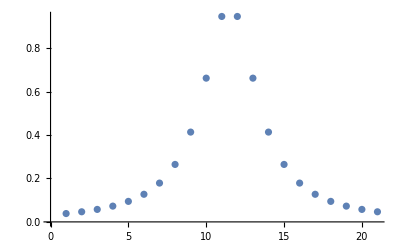

```mathematica
ListPlot[y[x]] /. x->punkty[20]
```

```mathematica
InterpolatingPolynomial[y[k],k]/.k->punpasskty[10]
```

InterpolatingPolynomial::list: List expected at position 1 in InterpolatingPolynomial[1/(1+25 k^2),k].

InterpolatingPolynomial::ipab: Abscissa specification 1 in {1,1/26} is not a point in 11 dimensions.

InterpolatingPolynomial[{1/26,121/2146,121/1346,121/746,121/346,121/146,121/146,121/346,121/746,121/1346,121/2146},{-1,-9/11,-7/11,-5/11,-3/11,-1/11,1/11,3/11,5/11,7/11,9/11}]

```mathematica
□
```

□

```mathematica
xcos[n_]:=Cos[(2*i+1)/(2*(n+1))*Pi]/.i->Array[#&,n+1,0]
```

```mathematica
Array[#&,11,0]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
ark[n_]:=Array[#&,n+1,0]
```

```mathematica
ark[10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
N[xcos[10]]
```

{0.989821,0.909632,0.75575,0.540641,0.281733,0.,-0.281733,-0.540641,-0.75575,-0.909632,-0.989821}

```mathematica
xcos[10]
```

{Cos[π/22],Cos[(3 π)/22],Cos[(5 π)/22],Sin[(2 π)/11],Sin[π/11],0,-Sin[π/11],-Sin[(2 π)/11],-Cos[(5 π)/22],-Cos[(3 π)/22],-Cos[π/22]}

```mathematica
y[10]
```

1/2501

```mathematica
y
```

y

```mathematica
y[x]/.x-> xcos[10]
```

{1/(1+25 Cos[π/22]^2),1/(1+25 Cos[(3 π)/22]^2),1/(1+25 Cos[(5 π)/22]^2),1/(1+25 Sin[(2 π)/11]^2),1/(1+25 Sin[π/11]^2),1,1/(1+25 Sin[π/11]^2),1/(1+25 Sin[(2 π)/11]^2),1/(1+25 Cos[(5 π)/22]^2),1/(1+25 Cos[(3 π)/22]^2),1/(1+25 Cos[π/22]^2)}

```mathematica
N[%]
```

{0.0392254,0.0461132,0.0654496,0.120376,0.335083,1.,0.335083,0.120376,0.0654496,0.0461132,0.0392254}

```mathematica
y[0.5]
```

0.137931

```mathematica
Clear[x, y]
```

```mathematica
Clear[xi]
```

```mathematica
Clear[l]
```

```mathematica
y[x_] := 1/(1+25*x^2)
```

```mathematica
y[0.5]
```

0.137931

```mathematica
Array[2+x, 5]/.i->3
```

{(2+x)[1],(2+x)[2],(2+x)[3],(2+x)[4],(2+x)[5]}

```mathematica
xi[n_]:=-1+2*(i/(n+1))/.i->Array[#&,n+1,0]
```

```mathematica
xi[5]
```

{-1,-2/3,-1/3,0,1/3,2/3}

```mathematica
N[%]
```

{-1.,-0.666667,-0.333333,0.,0.333333,0.666667}

```mathematica
func[x_]:=Function[{y}, x+y]
```

```mathematica
l[j_, xlist_]:=Function[{x}, Product[If[i≠j,(x-xlist[[j]])/(xlist[[i]]-xlist[[j]]),1],{i, 1, Length[xlist]}]]
```

```mathematica
l[2,xi[4]][0.5]
```

-9.5319

```mathematica
w[xlist_, func_]:=Function[{x},Sum[l[j,x]*func[xlist[[j]]], {j, 1, Length[xlist]}]]
```

```mathematica
wn5=w[xi[5],y]
```

Function[{x$},∑_(j=1)^Length[{-1,-2/3,-1/3,0,1/3,2/3}] l[j,x$] y[{-1,-2/3,-1/3,0,1/3,2/3}⟦j⟧]]

```mathematica
wn5[0.5]
```

1/26 Function[{x$},∏_(i=1)^Length[0.5] If[i≠1,(x$-0.5⟦1⟧)/(0.5⟦i⟧-0.5⟦1⟧),1]]+9/109 Function[{x$},∏_(i=1)^Length[0.5] If[i≠2,(x$-0.5⟦2⟧)/(0.5⟦i⟧-0.5⟦2⟧),1]]+9/34 Function[{x$},∏_(i=1)^Length[0.5] If[i≠3,(x$-0.5⟦3⟧)/(0.5⟦i⟧-0.5⟦3⟧),1]]+Function[{x$},∏_(i=1)^Length[0.5] If[i≠4,(x$-0.5⟦4⟧)/(0.5⟦i⟧-0.5⟦4⟧),1]]+9/34 Function[{x$},∏_(i=1)^Length[0.5] If[i≠5,(x$-0.5⟦5⟧)/(0.5⟦i⟧-0.5⟦5⟧),1]]+9/109 Function[{x$},∏_(i=1)^Length[0.5] If[i≠6,(x$-0.5⟦6⟧)/(0.5⟦i⟧-0.5⟦6⟧),1]]